# Interaction rate/ Collision term calculation

#### Following Appendix C of Dirac neutrinos and N_eff ( https://arxiv.org/abs/2005.01629 ) -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics- -Graphics-

## D Integrals

```mathematica
Dss=(4*λ^2 /Pi)*(p1*Sin[λ*p1]/(λ*p1)) *(p2*Sin[λ*p2]/(λ*p2)) *(p3*Sin[λ*p3]/(λ*p3)) *(p4*Sin[λ*p4]/(λ*p4)) 
Dsc =(4*p1*p2*p3*p4 /Pi)*λ^2*  Sin[λ*p1]/(λ*p1) Sin[λ*p2]/(λ*p2)((Cos[λ*p3]-( Sin[λ*p3]/(λ*p3)))/(p3*λ))(Cos[λ*p4]-( Sin[λ*p4]/(λ*p4)))/(p4*λ) 
Dcs =(4*p1*p2*p3*p4/Pi)*λ^2* ((Cos[λ*p1]-( Sin[λ*p1]/(λ*p1)))/(p1*λ))(Cos[λ*p2]-( Sin[λ*p2]/(λ*p2)))/(p2*λ)* Sin[λ*p3]/(λ*p3) Sin[λ*p4]/(λ*p4)
Dcc=(4*λ^2 /Pi)*(p1(Cos[λ*p1]-( Sin[λ*p1]/(λ*p1)))/(λ*p1))*(p2(Cos[λ*p2]-( Sin[λ*p2]/(λ*p2)))/(λ*p2))*(p3(Cos[λ*p3]-( Sin[λ*p3]/(λ*p3)))/(λ*p3))*(p4(Cos[λ*p4]-( Sin[λ*p4]/(λ*p4)))/(λ*p4))
```

(4 Sin[p1 λ] Sin[p2 λ] Sin[p3 λ] Sin[p4 λ])/(π λ^2)

(4 Sin[p1 λ] Sin[p2 λ] (Cos[p3 λ]-Sin[p3 λ]/(p3 λ)) (Cos[p4 λ]-Sin[p4 λ]/(p4 λ)))/(π λ^2)

(4 (Cos[p1 λ]-Sin[p1 λ]/(p1 λ)) (Cos[p2 λ]-Sin[p2 λ]/(p2 λ)) Sin[p3 λ] Sin[p4 λ])/(π λ^2)

(4 (Cos[p1 λ]-Sin[p1 λ]/(p1 λ)) (Cos[p2 λ]-Sin[p2 λ]/(p2 λ)) (Cos[p3 λ]-Sin[p3 λ]/(p3 λ)) (Cos[p4 λ]-Sin[p4 λ]/(p4 λ)))/(π λ^2)

#### General conditions

```mathematica
$Assumptions=p1 >0&& p2>0&&p3>0&& p4>0 && n∈Reals&& n>0&& p1∈Reals&&p2∈Reals&&p3∈Reals&& p4∈Reals && p1<p2+p3+p4&& p2<p1+p3+p4&& p3<p2+p1+p4&& p4<p2+p3+p1&& p1≠p2&& p3≠p4 &&p1≠p3&& p2≠p4 &&p3≠p2 &&p1≠p4
```

p1>0&&p2>0&&p3>0&&p4>0&&n∈ℝ&&n>0&&p1∈ℝ&&p2∈ℝ&&p3∈ℝ&&p4∈ℝ&&p1<p2+p3+p4&&p2<p1+p3+p4&&p3<p1+p2+p4&&p4<p1+p2+p3&&p1≠p2&&p3≠p4&&p1≠p3&&p2≠p4&&p3≠p2&&p1≠p4

#### First set of conditions p_1+p_2>p_3+p_4&p_1+p_4>p_2+p_3

```mathematica
AppendTo[$Assumptions,p1+p2>p3+p4 && p1+p4>p2+p3&& p1>p2&& p3≥p4 ]
```

p1>0&&p2>0&&p3>0&&p4>0&&n∈ℝ&&n>0&&p1∈ℝ&&p2∈ℝ&&p3∈ℝ&&p4∈ℝ&&p1<p2+p3+p4&&p2<p1+p3+p4&&p3<p1+p2+p4&&p4<p1+p2+p3&&p1≠p2&&p3≠p4&&p1≠p3&&p2≠p4&&p3≠p2&&p1≠p4&&p1+p2>p3+p4&&p1+p4>p2+p3&&p1>p2&&p3≥p4

```mathematica
Dss1=Integrate[Dss,{λ,0,Infinity}] 
Dsc1=Integrate[Dsc,{λ,0,Infinity}]
Dcs1=Integrate[Dcs,{λ,0,Infinity}] 
Dcc1=Integrate[Dcc,{λ,0,Infinity}]
```

1/2 (-p1+p2+p3+p4)

((-p1+p2+p3)^2 (p1-p2+2 p3)+3 (-p1+p2) p4^2+2 p4^3)/(12 p3 p4)

(-2 p1^3+3 p1^2 (p3+p4)+(2 p2-p3-p4) (p2+p3+p4)^2)/(12 p1 p2)

(p1^5-p2^5+5 p2^3 (p3^2+p4^2)-5 p1^3 (p2^2+p3^2+p4^2)-(p3+p4)^3 (p3^2-3 p3 p4+p4^2)+5 p2^2 (p3^3+p4^3)+5 p1^2 (p2^3+p3^3+p4^3))/(60 p1 p2 p3 p4)

```mathematica
$Assumptions=p1 >0&& p2>0&&p3>0&& p4>0 && n∈Reals&& n>0&& p1∈Reals&&p2∈Reals&&p3∈Reals&& p4∈Reals && p1<p2+p3+p4&& p2<p1+p3+p4&& p3<p2+p1+p4&& p4<p2+p3+p1&& p1≠p2&& p3≠p4 &&p1≠p3&& p2≠p4 &&p3≠p2 &&p1≠p4
```

p1>0&&p2>0&&p3>0&&p4>0&&n∈ℝ&&n>0&&p1∈ℝ&&p2∈ℝ&&p3∈ℝ&&p4∈ℝ&&p1<p2+p3+p4&&p2<p1+p3+p4&&p3<p1+p2+p4&&p4<p1+p2+p3&&p1≠p2&&p3≠p4&&p1≠p3&&p2≠p4&&p3≠p2&&p1≠p4

#### Second set of conditions p_1+p_2≥p_3+p_4&p_1+p_4<p_2+p_3

```mathematica
AppendTo[$Assumptions,p1+p2≥p3+p4 && p1+p4<p2+p3&& p1≥p2&& p3≥p4 ]
```

p1>0&&p2>0&&p3>0&&p4>0&&n∈ℝ&&n>0&&p1∈ℝ&&p2∈ℝ&&p3∈ℝ&&p4∈ℝ&&p1<p2+p3+p4&&p2<p1+p3+p4&&p3<p1+p2+p4&&p4<p1+p2+p3&&p1≠p2&&p3≠p4&&p1≠p3&&p2≠p4&&p3≠p2&&p1≠p4&&p1+p2≥p3+p4&&p1+p4<p2+p3&&p1≥p2&&p3≥p4

```mathematica
Dss2=Integrate[Dss,{λ,0,Infinity}] 
Dsc2=Integrate[Dsc,{λ,0,Infinity}]
Dcs2=Integrate[Dcs,{λ,0,Infinity}] 
Dcc2=Integrate[Dcc,{λ,0,Infinity}]
```

p4

p4^2/(3 p3)

-(p4 (-3 (p1^2+p2^2-p3^2)+p4^2))/(6 p1 p2)

-(-5 (p1^2+p2^2+p3^2) p4^2+p4^4)/(30 p1 p2 p3)

```mathematica
$Assumptions=p1 >0&& p2>0&&p3>0&& p4>0 && n∈Reals&& n>0&& p1∈Reals&&p2∈Reals&&p3∈Reals&& p4∈Reals && p1<p2+p3+p4&& p2<p1+p3+p4&& p3<p2+p1+p4&& p4<p2+p3+p1&& p1≠p2&& p3≠p4 &&p1≠p3&& p2≠p4 &&p3≠p2 &&p1≠p4
```

p1>0&&p2>0&&p3>0&&p4>0&&n∈ℝ&&n>0&&p1∈ℝ&&p2∈ℝ&&p3∈ℝ&&p4∈ℝ&&p1<p2+p3+p4&&p2<p1+p3+p4&&p3<p1+p2+p4&&p4<p1+p2+p3&&p1≠p2&&p3≠p4&&p1≠p3&&p2≠p4&&p3≠p2&&p1≠p4

#### Third set of conditions p_1+p_2<p_3+p_4&p_1+p_4<p_2+p_3

```mathematica
AppendTo[$Assumptions,p1+p2<p3+p4 && p1+p4<p2+p3&& p1≥p2&& p3≥p4 ]
```

p1>0&&p2>0&&p3>0&&p4>0&&n∈ℝ&&n>0&&p1∈ℝ&&p2∈ℝ&&p3∈ℝ&&p4∈ℝ&&p1<p2+p3+p4&&p2<p1+p3+p4&&p3<p1+p2+p4&&p4<p1+p2+p3&&p1≠p2&&p3≠p4&&p1≠p3&&p2≠p4&&p3≠p2&&p1≠p4&&p1+p2<p3+p4&&p1+p4<p2+p3&&p1≥p2&&p3≥p4

```mathematica
Dss3=Integrate[Dss,{λ,0,Infinity}] 
Dsc3=Integrate[Dsc,{λ,0,Infinity}]
Dcs3=Integrate[Dcs,{λ,0,Infinity}] 
Dcc3=Integrate[Dcc,{λ,0,Infinity}]
```

1/2 (p1+p2-p3+p4)

(-(p1+p2-p3)^2 (p1+p2+2 p3)+3 (p1+p2) p4^2+2 p4^3)/(12 p3 p4)

(2 p1^3+3 p1^2 (-p3+p4)+(2 p2+p3-p4) (p2-p3+p4)^2)/(12 p1 p2)

-1/(60 p1 p2 p3 p4)(p1^5-5 p1^3 (p2^2+p3^2-3 p3 p4+p4^2)+(p2-p3+p4)^3 (p2^2+p3^2+3 p2 (p3-p4)+3 p3 p4+p4^2)-5 p1^2 (p2^3-p3^3-9 p2 p3 p4+6 p3^2 p4-6 p3 p4^2+p4^3)+15 p1 p3 p4 (3 p2^2+(p3-p4)^2+4 p2 (3 p3+p4))-(15 p2 p3 p4 (p1+p4) (p1^2+(p2-p3+p4)^2+2 p1 (p2+3 p3+p4)) Abs[p1-p4])/Abs[p1^2-p4^2]-(15 p1 p3 p4 (p2+p4) (p1^2+p2^2+(p3-p4)^2+2 p1 (p2-p3+p4)+2 p2 (3 p3+p4)) Abs[p2-p4])/Abs[p2^2-p4^2])

```mathematica
$Assumptions=p1 >0&& p2>0&&p3>0&& p4>0 && n∈Reals&& n>0&& p1∈Reals&&p2∈Reals&&p3∈Reals&& p4∈Reals && p1<p2+p3+p4&& p2<p1+p3+p4&& p3<p2+p1+p4&& p4<p2+p3+p1&& p1≠p2&& p3≠p4 &&p1≠p3&& p2≠p4 &&p3≠p2 &&p1≠p4
```

p1>0&&p2>0&&p3>0&&p4>0&&n∈ℝ&&n>0&&p1∈ℝ&&p2∈ℝ&&p3∈ℝ&&p4∈ℝ&&p1<p2+p3+p4&&p2<p1+p3+p4&&p3<p1+p2+p4&&p4<p1+p2+p3&&p1≠p2&&p3≠p4&&p1≠p3&&p2≠p4&&p3≠p2&&p1≠p4

#### Fourth set of conditions p_1+p_2<p_3+p_4&p_1+p_4≥p_2+p_3

```mathematica
AppendTo[$Assumptions,p1+p2<p3+p4  && p1+p4≥p2+p3&& p1≥p2&& p3≥p4 ]
```

p1>0&&p2>0&&p3>0&&p4>0&&n∈ℝ&&n>0&&p1∈ℝ&&p2∈ℝ&&p3∈ℝ&&p4∈ℝ&&p1<p2+p3+p4&&p2<p1+p3+p4&&p3<p1+p2+p4&&p4<p1+p2+p3&&p1≠p2&&p3≠p4&&p1≠p3&&p2≠p4&&p3≠p2&&p1≠p4&&p1+p2<p3+p4&&p1+p4≥p2+p3&&p1≥p2&&p3≥p4

```mathematica
Dss4=Integrate[Dss,{λ,0,Infinity}] 
Dsc4=Integrate[Dsc,{λ,0,Infinity}]
Dcs4=Integrate[Dcs,{λ,0,Infinity}] 
Dcc4=Integrate[Dcc,{λ,0,Infinity}]
```

p2

-(p2 (3 p1^2+p2^2-3 (p3^2+p4^2)))/(6 p3 p4)

p2^2/(3 p1)

(p2^2 (5 p1^2-p2^2+5 (p3^2+p4^2)))/(30 p1 p3 p4)

-Graphics-
-Graphics-

#### First integration can be done by removing Dirac-delta function with p_4→ p_1+p_2-p_3

```mathematica
C4[p1_,p2_, p3_,T_]=(p2*p3*p4)/(32*p1*π^2)* 1/(ⅇ^(p2/T)+1)*(1-1/(ⅇ^(p3/T)+1))*(1-1/(ⅇ^(p4/T)+1))*(UnitStep[ p1+ p2-p3- p4 , p1+ p4- p2-p3 ]* (1/2 (-p1+p2+p3+p4)+((-p1+p2+p3)^2 (p1-p2+2 p3)+3 (-p1+p2) p4^2+2 p4^3)/(12 p3 p4)+(-2 p1^3+3 p1^2 (p3+p4)+(2 p2-p3-p4) (p2+p3+p4)^2)/(12 p1 p2)+ 1/(60 p1 p2 p3 p4)(p1^5-p2^5+5 p2^3 (p3^2+p4^2)-5 p1^3 (p2^2+p3^2+p4^2)-(p3+p4)^3 (p3^2-3 p3 p4+p4^2)+5 p2^2 (p3^3+p4^3)+5 p1^2 (p2^3+p3^3+p4^3)))+UnitStep[ p1+ p2-p3- p4 , p2+ p3- p1-p4 ]* (p4 +p4^2/(3 p3)-(p4 (-3 (p1^2+p2^2-p3^2)+p4^2))/(6 p1 p2)-(-5 (p1^2+p2^2+p3^2) p4^2+p4^4)/(30 p1 p2 p3))+UnitStep[ p3+ p4-p1- p2 , p2+ p3- p1-p4 ]* (1/2 (p1+p2-p3+p4)+(-(p1+p2-p3)^2 (p1+p2+2 p3)+3 (p1+p2) p4^2+2 p4^3)/(12 p3 p4)+(2 p1^3+3 p1^2 (-p3+p4)+(2 p2+p3-p4) (p2-p3+p4)^2)/(12 p1 p2)-1/(60 p1 p2 p3 p4)(p1^5-5 p1^3 (p2^2+p3^2-3 p3 p4+p4^2)+(p2-p3+p4)^3 (p2^2+p3^2+3 p2 (p3-p4)+3 p3 p4+p4^2)-5 p1^2 (p2^3-p3^3-9 p2 p3 p4+6 p3^2 p4-6 p3 p4^2+p4^3)+15 p1 p3 p4 (3 p2^2+(p3-p4)^2+4 p2 (3 p3+p4))-(15 p2 p3 p4 (p1+p4) (p1^2+(p2-p3+p4)^2+2 p1 (p2+3 p3+p4)))/Abs[p1+p4]-(15 p1 p3 p4 (p2+p4) (p1^2+p2^2+(p3-p4)^2+2 p1 (p2-p3+p4)+2 p2 (3 p3+p4)))/Abs[p2+p4]))+UnitStep[ p3+ p4-p1- p2 , p1+p4-p2-p3]*(p2-(p2 (3 p1^2+p2^2-3 (p3^2+p4^2)))/(6 p3 p4)+p2^2/(3 p1)+(p2^2 (5 p1^2-p2^2+5 (p3^2+p4^2)))/(30 p1 p3 p4) ) )/. p4-> p1+ p2-p3 ;
```

#### Second integration over p_3 is done numerically

```mathematica
C34[p1_?NumericQ, p2_?NumericQ,T_?NumericQ]:=Chop[NIntegrate[C4[p1,p2, p3,T],{p3,0.0,p1+p2},
Method->{"AdaptiveQuasiMonteCarlo","MaxPoints"->10^9},AccuracyGoal->6,MaxRecursion->40],10^-30]//Quiet
C34[0.01,10,0.01]//AbsoluteTiming
```

{0.149387,0}

#### Final integration over p_2 is again done numerically but to speed up the integration, C34 is interpolated and then integrated.

```mathematica
gamma[p_?NumericQ,T_?NumericQ]:= NIntegrate[Interpolation[Chop[ParallelTable[{10^n,C34[p,10^n,T]},{n,-5,2.1,0.05}],10^-30]][p2],{p2,0,∞},
Method->{"AdaptiveQuasiMonteCarlo","MaxPoints"->10^9},AccuracyGoal->10,MaxRecursion->40]//Quiet
```

```mathematica
(*Final integration over Subscript[p, 2] without using interpolation*)
C234[p_?NumericQ,T_?NumericQ]:=NIntegrate[C34[p, p2,T],{ p2,0.0,100},
Method->{"AdaptiveQuasiMonteCarlo","MaxPoints"->10^9},AccuracyGoal->6,MaxRecursion->40]
```

```mathematica
C234[0.1,0.4]//AbsoluteTiming (*Time difference between integration of C23 and integration of interpolated C23*)
gamma[0.1,0.4]//AbsoluteTiming
```

{32.3124,0.0494218}

{1.57813,0.0494185}

#### Interaction rate in SM without G_F ; C_α pT^4

```mathematica
Cedata = Import[NotebookDirectory[]<>"C_e.txt", "Table"];
Ce=Interpolation[Cedata, InterpolationOrder->1];
```

```mathematica
smgamma[p_,T_]:=Ce[T]* p*T^4
```

#### Comparison between Γ_NSI and Γ_SM (also checking T dependence of new interaction rate)

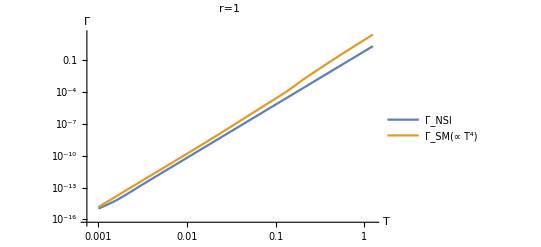

```mathematica
ListLogLogPlot[{Table[{10^n,gamma[10^n,10^n]},{n,-3,0.1,0.1}],Table[{10^n,smgamma[10^n,10^n]},{n,-3,.1,0.1}]},Joined-> True,PlotStyle->Thick,PlotLegends-> {"Γ_NSI","Γ_SM(∝ T^4)"},AxesLabel->{"T","Γ"},PlotLabel->"r=1"]
```

```mathematica
ListLogLogPlot[{Table[{10^n,gamma[10^n,10^n]},{n,-3,0.1,0.1}],Table[{10^n,gamma[0.1*10^n,10^n]},{n,-3,0.1,0.1}],Table[{10^n,gamma[0.01*10^n,10^n]},{n,-3,0.1,0.1}],Table[{10^n,smgamma[0.01*10^n,10^n]},{n,-3,0.1,0.1}]},Joined-> True,PlotLegends-> {"r=1","r=0.1","r=0.01","Γ_SM(r=0.01)"},AxesLabel->{"T","Γ"},PlotLabel->"Γ_NSI"]
```

$Aborted

### p Vs Γ_NSI (at different temperatures)

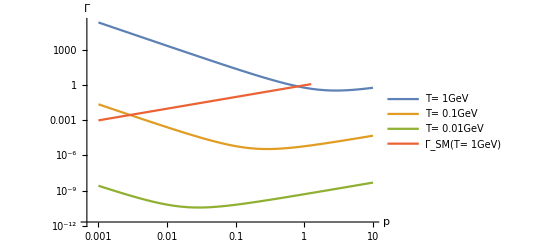

```mathematica
ListLogLogPlot[{Table[{10^n,gamma[10^n,1]},{n,-3,1,0.1}],Table[{10^n,gamma[10^n,0.1]},{n,-3,1,0.1}],Table[{10^n,gamma[10^n,0.01]},{n,-3,1,0.1}],Table[{10^n,smgamma[10^n,1]},{n,-3,.1,0.1}]},PlotLegends-> {"T= 1GeV","T= 0.1GeV","T= 0.01GeV","Γ_SM(T= 1GeV)"},AxesLabel->{"p","Γ"},Joined->True]
```

### C_α(T)

#### SM

-Graphics-

#### If Γ_NSI= C*G_F*p*T^4

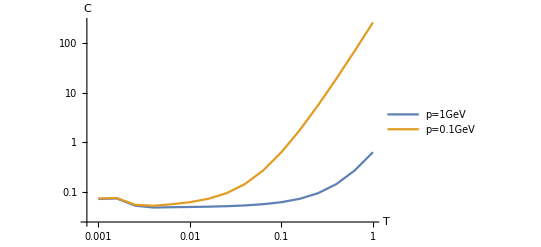

```mathematica
ListLogLogPlot[{Table[{10^n,gamma[1,10^n]/(1*(10^n)^4)},{n,-3,0,0.2}],Table[{10^n,gamma[.1,10^n]/(.1*(10^n)^4)},{n,-3,0,0.2}]},PlotLegends-> {"p=1GeV","p=0.1GeV"},AxesLabel->{"T","C(T)"},Joined->True]
```

### Problems with extreme values

```mathematica
gamma[0.2,0.2]
gamma[0.2,20] (*Large T(>1GeV) *)
gamma[0.0002,0.2](*Small p*)
gamma[0.0002,20](*Small p, Large T*)
```

0.00020032

-1.24713×10^64

75.372

-6.42088×10^70

#### Γ_NSI/H=Γ_NSI/T^2*M_pl∼ 10^22×10^-10×ϵ^2×T^2